#### A部分：处理从 Web 导入的数据

从 CSV 文件加载一些数据并将其显示为数据集：

```mathematica
data=Dataset[Import["https://data.nasa.gov/api/views/gh4g-9sfh/rows.csv","HeaderLines"-> 1]]
```

Dataset[<>]

显示数据集第五列中的条目：

```mathematica
data[All,5]
```

Dataset[<>]

计算第 5 列中所有值的对数：

```mathematica
data[Log,5]
```

Dataset[<>]

制作数据第 5 列中所有条目的对数的直方图：

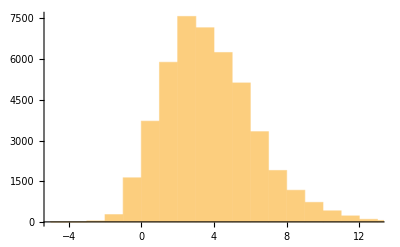

```mathematica
data[Log/* Histogram,5]
```

为第 4 列中的条目制作词云：

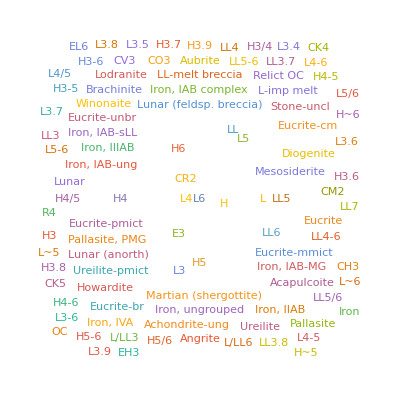

```mathematica
data[WordCloud,4]
```